WHY DOES JPEG USE THE DISCRETE COSINE TRANSFORM RATHER THAN JUST THE DISCRETE FOURIER TRANSFORM?
(to accompany the Lecture Notes)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ignjat/Dropbox/4_COURSES/4121/00_New_Lecture_Notes/_2019/11_DFT_DCT_CONV/Mathematica

Lets consider the following sequence of M samples of a signal

```mathematica
M=32;
```

```mathematica
signal1[t_]:=Cos[(2π  3t)/M +2] +2 Cos[ (2π  7t)/M-1];
```

```mathematica
Samp1=Table[N[signal1[t]],{t,0,M-1}];
```

Note that N[...] forces Mathematica to evaluate functions, rather than keeping them as symbolic expressions which is slower. For plotting purposes we also form a table of pairs of (x, y) coordinates:

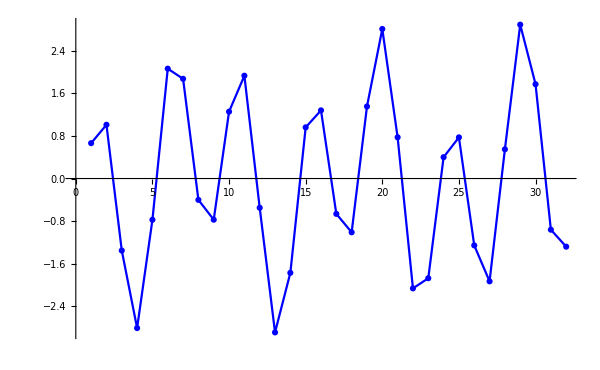

```mathematica
PlotSamp=ListPlot[Samp1,Joined-> True,FillingStyle->Automatic,PlotMarkers->Automatic,PlotStyle-> {Blue},ImageSize-> 600]
```

Let us take its Discrete Fourier Transform and plot its absolute value (recall that DFT is in general a complex valued sequence). We start with the matrix of the conjugates of the roots of unity:

```mathematica
DFT1=Chop[Table[1/(√M)∑_(j=0)^(M-1) Samp1[[j+1]] ⅇ^(-ⅈ (2π j k)/M),{k,0,M-1}]]
```

{0,0,0,-1.17704+2.57188 ⅈ,0,0,0,3.05641-4.76008 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.05641+4.76008 ⅈ,0,0,0,-1.17704-2.57188 ⅈ,0,0}

Lets plot its absolute values:

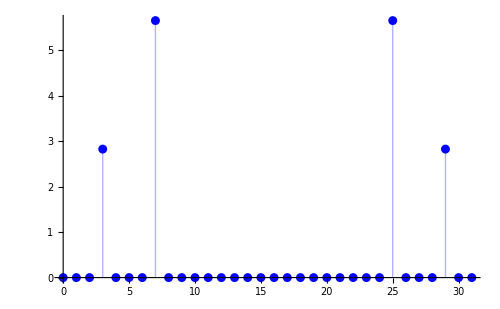

```mathematica
PlotFourier1=ListPlot[Table[{k,Abs[DFT1[[k+1]]]},{k,0,M-1}],Filling->Axis,FillingStyle->Automatic,PlotRange-> All,PlotStyle-> {Blue},ImageSize-> 500]
```

Note that there are 4 peaks because we need two complex exponentials for each sinusoids to cancel out imaginary parts:  (ĉ)_(n-m) ⅇ^(ⅈ (2π)/n k (n-m)) = Conjugate[ (ĉ)_m ⅇ^(ⅈ (2π)/n k m)];

Now consider instead the following sequence of M samples of  another signal, and plot them:

```mathematica
signal2[t_]:=Cos[(2π  1.35t)/M+2]+2Cos[(2π  4.05t)/M-2];
```

```mathematica
Samp2=Table[N[signal2[t]],{t,0,M-1}];
```

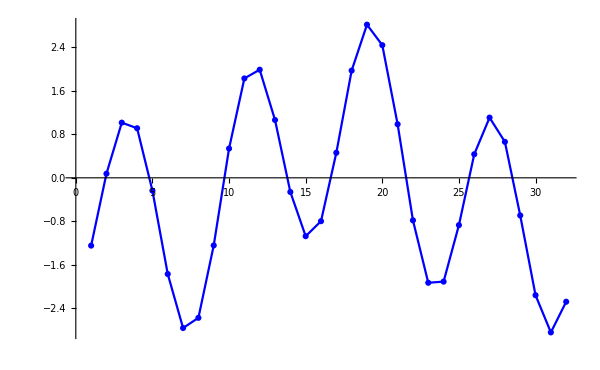

```mathematica
Plot2=ListPlot[Samp2,Joined-> True,PlotStyle-> {Blue},PlotMarkers->Automatic,ImageSize-> 600]
```

Let us take the Discrete Fourier Transform of that sequence and plot its  absolute values:

```mathematica
DFT2=Chop[Table[1/(√M)∑_(j=0)^(M-1) Samp2[[j+1]] ⅇ^(-ⅈ (2π j k)/M),{k,0,M-1}]]
```

{-1.26247,-2.70849+0.0451564 ⅈ,0.90672-0.152603 ⅈ,0.181111-0.25287 ⅈ,-1.40838-5.41804 ⅈ,0.127447+0.29297 ⅈ,0.0575727+0.144542 ⅈ,0.0279063+0.0950242 ⅈ,0.0112262+0.0692311 ⅈ,0.0007388+0.0527689 ⅈ,-0.00626152+0.0409161 ⅈ,-0.011089+0.0316557 ⅈ,-0.0144562+0.0239695 ⅈ,-0.0167753+0.0172772 ⅈ,-0.0182923+0.0112123 ⅈ,-0.0191518+0.00551932 ⅈ,-0.0194304,-0.0191518-0.00551932 ⅈ,-0.0182923-0.0112123 ⅈ,-0.0167753-0.0172772 ⅈ,-0.0144562-0.0239695 ⅈ,-0.011089-0.0316557 ⅈ,-0.00626152-0.0409161 ⅈ,0.0007388-0.0527689 ⅈ,0.0112262-0.0692311 ⅈ,0.0279063-0.0950242 ⅈ,0.0575727-0.144542 ⅈ,0.127447-0.29297 ⅈ,-1.40838+5.41804 ⅈ,0.181111+0.25287 ⅈ,0.90672+0.152603 ⅈ,-2.70849-0.0451564 ⅈ}

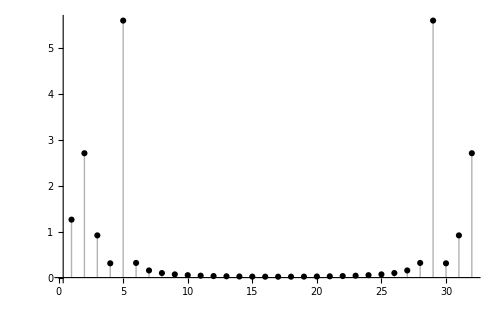

```mathematica
PlotAbsDFT2=ListPlot[{Abs[DFT2]},Filling->Axis,PlotStyle-> {Black},FillingStyle->Automatic,PlotRange-> All,PlotMarkers->Automatic,ImageSize-> 500]
```

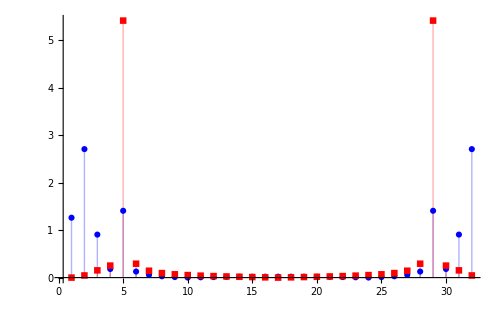

```mathematica
PlotDFT2=ListPlot[{Abs[Re[DFT2]],Abs[Im[DFT2]]},Filling->Axis,PlotStyle-> {Blue,Red},FillingStyle->Automatic,PlotRange-> All,PlotMarkers->Automatic,ImageSize-> 500]
```

So, since now the frequencies  2π 1.35/M  and  2π 4.05/M  fall between the bin frequencies of the DFT, for each frequency we get several peaks. Let us now compress such a signal by keeping only 8 floating point largest numbers (either real or imaginary parts of the DFT of such a signal).

```mathematica
Kth=8;
```

```mathematica
T2=DFT2[[1;;Floor[M/2]+1]];
T21=Abs[Re[T2]];
```

```mathematica
T22=Abs[Im[T2]];
```

```mathematica
TT2=Join[T21,T22];
```

```mathematica
TTT2=Sort[TT2,Greater];
```

```mathematica
KthElement1=TTT2[[Kth]];
```

```mathematica
CompDFT2=DFT2[[1;;Floor[M/2]+1]];
```

```mathematica
Do[If[Abs[Re[CompDFT2[[i]]]]<KthElement1,CompDFT2[[i]]=ⅈ Im[CompDFT2[[i]]]],{i,1,Floor[M/2]+1}]
```

```mathematica
Do[If[Abs[Im[CompDFT2[[i]]]]< KthElement1,CompDFT2[[i]]=Re[CompDFT2[[i]]]],{i,1,Floor[M/2]+1}];
```

```mathematica
Transpose[{DFT2[[1;;Floor[M/2]+1]],CompDFT2}]//MatrixForm
```

(-1.26247 | -1.26247
-2.70849+0.0451564 ⅈ | -2.70849
0.90672-0.152603 ⅈ | 0.90672
0.181111-0.25287 ⅈ | 0.181111-0.25287 ⅈ
-1.40838-5.41804 ⅈ | -1.40838-5.41804 ⅈ
0.127447+0.29297 ⅈ | 0.+0.29297 ⅈ
0.0575727+0.144542 ⅈ | 0.
0.0279063+0.0950242 ⅈ | 0.
0.0112262+0.0692311 ⅈ | 0.
0.0007388+0.0527689 ⅈ | 0.
-0.00626152+0.0409161 ⅈ | 0.
-0.011089+0.0316557 ⅈ | 0.
-0.0144562+0.0239695 ⅈ | 0.
-0.0167753+0.0172772 ⅈ | 0.
-0.0182923+0.0112123 ⅈ | 0.
-0.0191518+0.00551932 ⅈ | 0.
-0.0194304 | 0)

```mathematica
ConCompDFT2=ConstantArray[0,Floor[M/2]-1];
```

```mathematica
Do[ConCompDFT2[[n]]=Conjugate[CompDFT2[[Floor[M/2]+1-n]]],{n,1,Floor[M/2]-1}]
```

```mathematica
CompressDFT2=Join[CompDFT2,ConCompDFT2];
```

```mathematica
InverseCompressDFT2=Table[1/(√M)∑_(j=0)^(M-1) CompressDFT2[[j+1]] ⅇ^(ⅈ (2π j k)/M),{k,0,M-1}];
```

```mathematica
Error2=Abs[InverseCompressDFT2-Samp2];
```

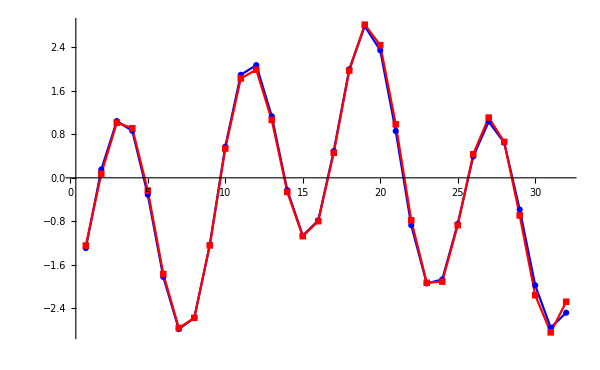

```mathematica
PLT2=ListPlot[{InverseCompressDFT2,Samp2},Joined-> True, PlotStyle->{Blue,Red},PlotRange-> All,ImageSize-> 600, PlotMarkers-> Automatic]
```

```mathematica
signal3[t_]:=Cos[(2π  1.34t)/M]+2Cos[(2π  3.5t)/M];
```

```mathematica
Samp3=Table[N[signal3[t]],{t,0,M-1}];
```

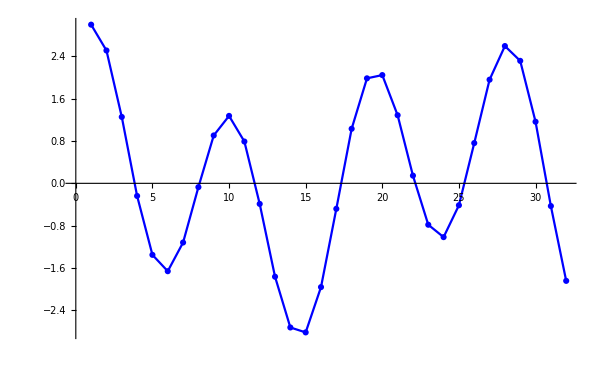

```mathematica
Plot3=ListPlot[Samp3,Joined-> True,PlotStyle-> {Blue},PlotMarkers->Automatic,ImageSize-> 600]
```

Let us take the Discrete Fourier Transform of that sequence and plot its  absolute values

```mathematica
DFT3=Chop[Table[1/(√M)∑_(j=0)^(M-1) Samp3[[j+1]] ⅇ^(-ⅈ (2π j k)/M),{k,0,M-1}]];
```

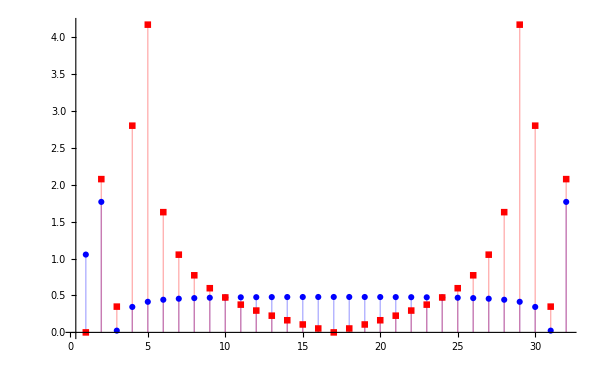

```mathematica
PlotDFT3=ListPlot[{Abs[Re[DFT3]],Abs[Im[DFT3]]},Filling->Axis,PlotStyle-> {Blue,Red},FillingStyle->Automatic,PlotRange-> All,PlotMarkers->Automatic,ImageSize-> 600]
```

```mathematica
GraphicsGrid[{{PlotDFT3,PlotDFT2}},ImageSize-> 1000]
```

So, since now the frequencies  2π 3.5/M  and  2π 7.5/M  fall between the bins 3 and 4 and between 7 and 8, respectively, of the DFT, for each frequency we get two peaks, but it appears that suddenly we also get a whole bunch of frequencies not present in the original signal!  As a consequence, this signal is not well compressible:

```mathematica
T3=DFT3[[1;;Floor[M/2]+1]];
T31=Abs[Re[T3]];
```

```mathematica
T32=Abs[Im[T3]];
```

```mathematica
TT3=Join[T31,T32];
```

```mathematica
TTT3=Sort[TT3,Greater];
```

```mathematica
KthElement3=TTT3[[Kth]];
```

```mathematica
CompDFT3=DFT3[[1;;Floor[M/2]+1]];
```

```mathematica
Do[If[Abs[Re[CompDFT3[[i]]]]<KthElement3,CompDFT3[[i]]=ⅈ Im[CompDFT3[[i]]]],{i,1,Floor[M/2]+1}]
```

```mathematica
Do[If[Abs[Im[CompDFT3[[i]]]]< KthElement3,CompDFT3[[i]]=Re[CompDFT3[[i]]]],{i,1,Floor[M/2]+1}];
```

```mathematica
ConCompDFT3=ConstantArray[0,Floor[M/2]-1];
```

```mathematica
Do[ConCompDFT3[[n]]=Conjugate[CompDFT3[[Floor[M/2]+1-n]]],{n,1,Floor[M/2]-1}]
```

```mathematica
CompressDFT3=Join[CompDFT3,ConCompDFT3];
```

```mathematica
InverseCompressDFT3=Table[1/(√M)∑_(j=0)^(M-1) CompressDFT3[[j+1]] ⅇ^(ⅈ (2π j k)/M),{k,0,M-1}];
```

```mathematica
Error3=Abs[InverseCompressDFT3-Samp3];
```

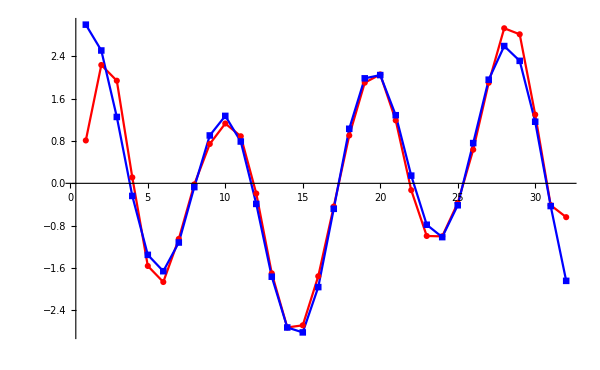

```mathematica
PLT3=ListPlot[{InverseCompressDFT3,Samp3}, PlotStyle->{Red,Blue},PlotRange-> All, Joined-> True, PlotMarkers-> Automatic,ImageSize-> 600]
```

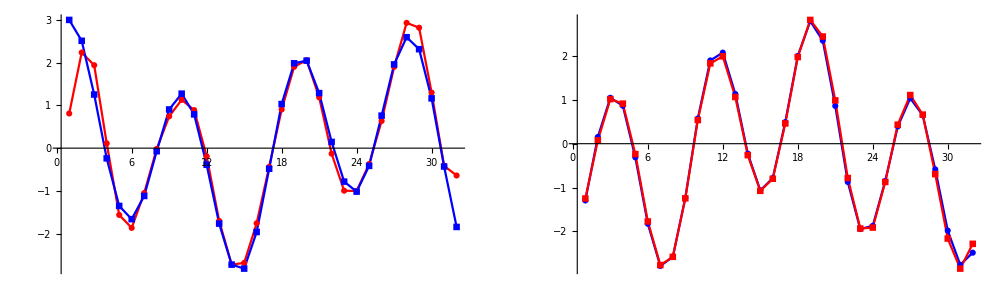

```mathematica
GraphicsGrid[{{PLT3,PLT2}},ImageSize-> 1000]
```

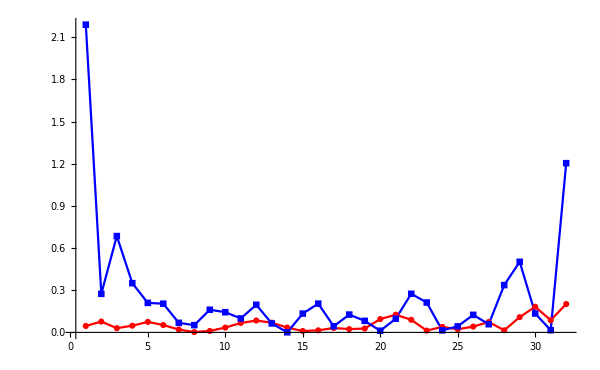

```mathematica
P3=ListPlot[{Error2,Error3},Joined-> True, PlotStyle->{Red,Blue},PlotRange-> All, PlotMarkers-> Automatic,ImageSize-> 600]
```

To understand that, let us represent the signal in the Fourier basis:

```mathematica
F2[t_]:=1/(√M)∑_(j=0)^(M-1) DFT2[[j+1]] ⅇ^(ⅈ (2π j t)/M);  
F3[t_]:=1/(√M)∑_(j=0)^(M-1) DFT3[[j+1]] ⅇ^(ⅈ (2π j t)/M);
```

Let us evaluate it over  over TWO complete periods, i.e., instead of from 0 to M-1 let us evaluate it from 0 to 2M-1:

```mathematica
Reconstruct2=Table[{k,F2[k]},{k,0,2M-1}];
```

```mathematica
Reconstruct3=Table[{k,F3[k]},{k,0,2M-1}];
```

Let us plot  values for k=0..M-1 in red and values k=M..2M-1  in blue, both for the first signal (Samp1) and the second signal (Samp2).

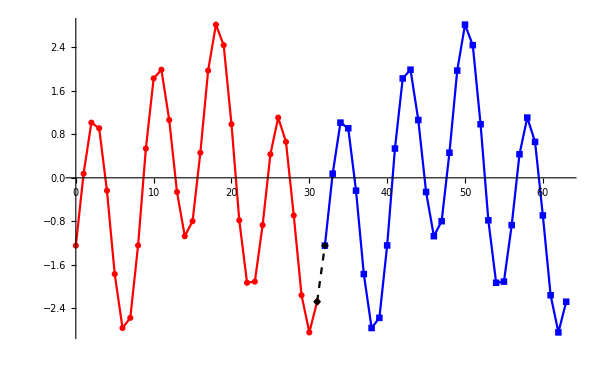

```mathematica
PD2=ListPlot[{Reconstruct2[[1;;M]],Reconstruct2[[M+1;;2M]],Reconstruct2[[M;;M+1]]},Joined-> True,PlotRange-> All,PlotStyle-> {Red,Blue,{Black,Dashed}},PlotMarkers->Automatic,ImageSize-> 600]
```

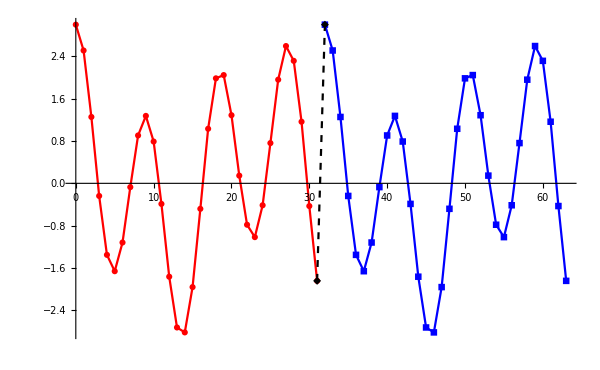

```mathematica
PD3=ListPlot[{Reconstruct3[[1;;M]],Reconstruct3[[M+1;;2M]],Reconstruct3[[M;;M+1]]},Joined-> True,PlotRange-> All,PlotStyle-> {Red,Blue,{Black,Dashed}},PlotMarkers->Automatic,ImageSize-> 600]
```

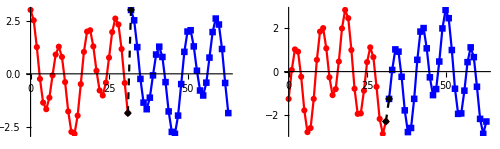

```mathematica
GraphicsGrid[{{PD3,PD2}},ImageSize->500]
```

The difference is that on the first plot the transition between the two periods is smooth, because the last sample and the first sample are not far away. However, in the second case there is a big jump from the last sample back to the first sample. This is what produces most of these spurious frequencies: the values at the end points differ a lot and the IDFT has to make a very large jump.

How can we remedy this? This is what the Discrete Cosine Transform does, and more!
Trick: Let us make another copy of the signal samples by flipping the original values around: and concatenate it to the original signal:

```mathematica
SampFlip=Join[Samp3,Table[Samp3[[M-j]],{j,0,M-1}]];
```

For plotting purposes only, we set:

```mathematica
val2=Table[{j,Samp3[[j+1]]},{j,0,M-1}];
```

```mathematica
val3=Table[{M+j,Samp3[[M-j]]},{j,0,M-1}];
```

```mathematica
val4={{M-1,Samp3[[M]]},{M,Samp3[[M]]}};
```

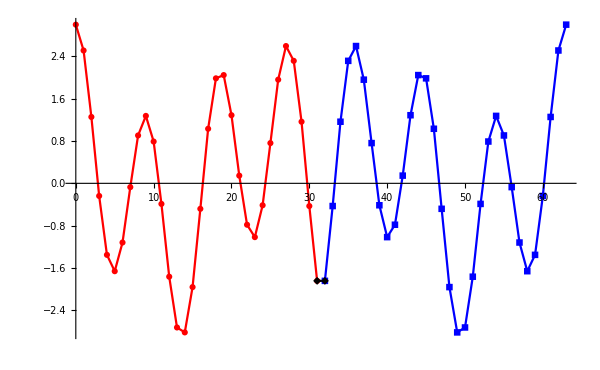

```mathematica
ListPlot[{val2,val3,val4},Joined-> True,PlotStyle-> {Red,Blue,Black},PlotMarkers->Automatic,ImageSize-> 600]
```

The left and the right end of such an extended signal match perfectly! We now take the DFT of such a signal; since we have twice as many points now, we need a lager matrix of the roots of unity:

```mathematica
DFT33=Chop[Table[1/(√(2M))∑_(j=0)^(2M-1) SampFlip[[j+1]] ⅇ^(-ⅈ (2π j k)/(2M)),{k,0,2M-1}]];
```

We plot the absolute value of the DFT of such extended sequence:

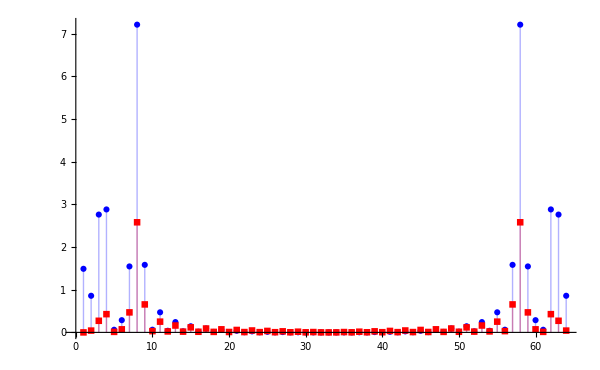

```mathematica
PlotDFT33=ListPlot[{Abs[Re[DFT33]],Abs[Im[DFT33]]},PlotRange-> All,Filling->Axis,FillingStyle->Automatic,PlotMarkers->Automatic,PlotStyle-> {Blue,Red},ImageSize-> 600]
```

```mathematica
GraphicsGrid[{{PlotDFT33,PlotDFT3}},ImageSize->1000]
```

Suddenly, most of the “ghost frequencies” have disappeared, but we have twice as many points. However, there has to be a lot of redundancy there because the extra points have come from a mirror copy of the original. More over, the DFTs of the extended signal is still complex valued, but “barely so”: note that in

```mathematica
SampFlip
```

for k=0 to k=2M-1  SampFlip[k]=SampFlip[2M-1-k] and the corresponding values of the Fourier kernel are       ⅇ^(-ⅈ (2π m k)/(2MM))    and     ⅇ^(-ⅈ (2π m(2MM-1- k))/(2MM)); thus, in the sum we get      SampFlip[k]ⅇ^(-ⅈ (2π m k)/(2MM))+SampFlip[2M-1-k]ⅇ^(-ⅈ (2π m(2MM-1- k))/(2MM))=SampFlip[k](ⅇ^(-ⅈ (2π m k)/(2MM))+ⅇ^(-ⅈ (2π m(2MM-1- k))/(2MM))); however,

```mathematica
ComplexExpand[ExpToTrig[ⅇ^(-ⅈ (2π m k)/(2MM))+ⅇ^(-ⅈ (2π m(2MM-1- k))/(2MM))]]
```

Cos[(k m π)/MM]+Cos[(m (-1-k+2 MM) π)/MM]+ⅈ (-Sin[(k m π)/MM]-Sin[(m (-1-k+2 MM) π)/MM])

Simplifying the imaginary part we get

```mathematica
FullSimplify[(-Sin[(m k π)/MM]-Sin[(m (-1-k+2 MM) π)/MM])==-2 Cos[(m (-1-2 k+2 MM) π)/(2 MM)] Sin[ π m(1-1/(2 MM))]]
```

True

Note that the imaginary part is “almost “ zero; if instead of Sin[ π m(1-1/(2 MM))] we had Sin[ π m] it would be zero.

So we fix this problem by slightly rotating the Fourier kernel by multiplying it with ⅇ^(-ⅈ π/(2MM)):

```mathematica
FullSimplify[ComplexExpand[ExpToTrig[(ⅇ^(-ⅈ (2π m k)/(2MM))+ⅇ^(-ⅈ (2π m(2MM-1- k))/(2MM)))ⅇ^(-ⅈ π/(2MM) m)]],Assumptions->MM∈Integers&&k∈Integers&&m∈Integers&&k<MM&&m<MM]
```

2 Cos[((1+2 k) m π)/(2 MM)]

```mathematica
FullSimplify[ComplexExpand[ExpToTrig[(ⅇ^(-ⅈ (2π m (k+1/2))/(2MM))+ⅇ^(-ⅈ (2π m(2MM-1- k+1/2))/(2MM)))]],Assumptions->MM∈Integers&&k∈Integers&&m∈Integers&&k<MM&&m<MM]
```

2 Cos[((1+2 k) m π)/(2 MM)]

To verify:

```mathematica
DCOST=Chop[Table[DFT33[[m+1]] ⅇ^(-ⅈ π/(2M)m),{m,0,2M-1}]];
```

```mathematica
DCOST[[M+1]]
```

Note that now all coordinates are real and that DCT[k+1]= - DCT[2M-k+1] for all  k such that 1≤ k ≤ 2M-1:

```mathematica
Chop[Table[DCOST[[k+1]]+DCOST[[2M-k+1]],{k,1,M}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

This is because the coordinates are symmetric : SampFlip[k]=SampFlip[2M-1-k] and

```mathematica
FullSimplify[Cos[(( k+1/2) (2MM-m) π)/MM]==-Cos[ (( k+1/2) m π)/MM],Assumptions->MM∈Integers&&k∈Integers&&m∈Integers&&k<MM&&m<MM]
```

Thus, we need to keep only the first M many values, i.e.  we let

```mathematica
DCT1=DCOST[[1;;M]];
```

Instead of first taking the DFT of the extended signal and then multiplying it with  ω_(2M) taken to the power -1/2 k, one can go directly by using a slightly different but still an orthonormal transform matrix; lets do it first for m=8 so that the matrix fits on paper:

```mathematica
m=8;
```

```mathematica
DCTMat=Table[1/(√(2m))ⅇ^(-ⅈ (π (j +1/2)k)/m),{j,0,2m-1},{k,0,2m-1}];
```

Complex conjugate transpose of this matrix (normalised by a factor of 1/(2m)) is:

```mathematica
IDCTMat=Table[1/(√(2m))ⅇ^(ⅈ (π (k+1/2)j)/m),{j,0,2m-1},{k,0,2m-1}];
```

Verifying that the conjugate transpose is again the inverse of T:

```mathematica
FullSimplify[IDCTMat.DCTMat]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

To verify that we get the same result as before let us compute such alternative discrete transform

```mathematica
DCT3=Table[Chop[∑_(j=0)^(2M-1) SampFlip[[j+1]] ⅇ^(-ⅈ (π (j +1/2)k)/M) ],{k,0,M-1}];
```

and compare it with what we got before:

```mathematica
NumberForm[{DCT1,1/(√(2M))DCT3}//MatrixForm,3]
```

(DCT1
{1.49,-0.859,2.77,2.91,-0.0631,0.295,1.61,7.66,-1.71,0.0695,-0.534,0.0442,-0.29,0.0303,-0.186,0.0217,-0.129,0.0161,-0.093,0.0121,-0.0686,0.00911,-0.0508,0.0068,-0.0371,0.00493,-0.026,0.00335,-0.0166,0.00194,-0.00806,0.000637})

The sequence  DCT is called the Discrete Cosine Transform of Type II  of the sequence Samp2.

```mathematica
InvDCT=Chop[Table[1/(2M)∑_(j=0)^(2M-1) DCOST[[j+1]] ⅇ^(ⅈ (π (k +1/2)j)/M),{k,0,2M-1}]];
```

The computation of the DCT of type II can further be simplified by using the following formula:

```mathematica
dct=Table[N[2∑_(j=0)^(M-1) Samp3[[j+1]]Cos[(π (j +1/2)k)/M] ],{k,0,M-1}];
```

For the Inverse Discrete Cosine Transform  (IDCT) we use

```mathematica
idct=Table[Chop[1/M(dct[[1]]/2+∑_(j=1)^(M-1) dct[[j+1]]Cos[(π (k +1/2)j)/M] )],{k,0,M-1}];
```

```mathematica
idct
```

{3.,2.51161,1.25489,-0.238469,-1.3523,-1.66139,-1.11899,-0.0716245,0.905172,1.27498,0.790443,-0.388983,-1.76524,-2.72522,-2.81829,-1.96187,-0.481754,1.03152,1.98513,2.0466,1.28787,0.145705,-0.782876,-1.01709,-0.414707,0.760906,1.95965,2.59556,2.31569,1.16477,-0.42944,-1.84381}

```mathematica
Samp3
```

{3.,2.51161,1.25489,-0.238469,-1.3523,-1.66139,-1.11899,-0.0716245,0.905172,1.27498,0.790443,-0.388983,-1.76524,-2.72522,-2.81829,-1.96187,-0.481754,1.03152,1.98513,2.0466,1.28787,0.145705,-0.782876,-1.01709,-0.414707,0.760906,1.95965,2.59556,2.31569,1.16477,-0.42944,-1.84381}

```mathematica
Chop[idct-Samp3]
```

Let us plot the DCT of Samp3:

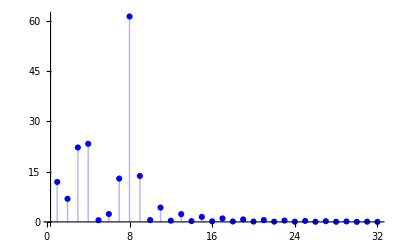

```mathematica
Plotdct=ListPlot[Abs[DCT3],Filling->Axis,FillingStyle->Automatic,PlotRange-> All,PlotMarkers->Automatic,PlotStyle-> {Blue}]
```

```mathematica
xre=Table[{i,Abs[Re[DFT3[[i]]]]},{i,0,Floor[M/2]-1}];xim=Table[{i+Floor[M/2],Abs[Im[DFT3[[i]]]]},{i,0,Floor[M/2]-1}];
```

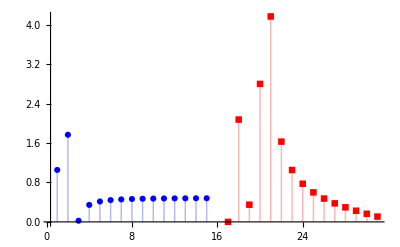

```mathematica
PlotDFT3RI=ListPlot[{xre,xim},Filling->Axis,FillingStyle->Automatic,PlotRange-> All,PlotMarkers->Automatic,PlotStyle-> {Blue,Red}]
```

We can now compare the values of the real and complex part of DFT  with the values of DCT which is always real:

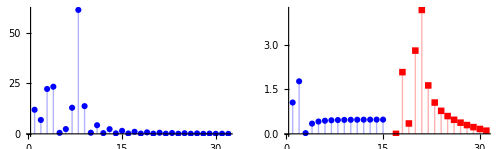

```mathematica
GraphicsGrid[{{Plotdct, PlotDFT3RI}},ImageSize->500]
```

Let us now do some signal compression: let us take k many largest (by the absolute value) numbers appearing in FR2 which is the DFT of Samp2 and set all others to 0:

```mathematica
KthElement2=Sort[Abs[DCT3],Greater][[Kth]]
```

4.26863

```mathematica
CompressDCT3=DCT3; Do[If[Abs[CompressDCT3[[i]]]<KthElement2,CompressDCT3[[i]]=0],{i,1,M}];
```

```mathematica
NumberForm[CompressDCT3,3]
```

{11.9,-6.87,22.2,23.3,0,0,12.9,61.3,-13.7,0,-4.27,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

And now  the inverse transforms of the compressed version of the DCT of the signal Samp3

```mathematica
InverseCompressDCT3=Table[Chop[1/M(CompressDCT3[[1]]/2+∑_(j=1)^(M-1) CompressDCT3[[j+1]]Cos[(π (k +1/2)j)/M] )],{k,0,M-1}];
```

Let us plot both and compare them with the original signal:

```mathematica
DecompressDCT=ListPlot[{Samp3,InverseCompressDCT3},Joined-> True,PlotStyle-> {Red,Blue}];
```

```mathematica
DecompressDFT=ListPlot[{Samp3,InverseCompressDFT3},Joined-> True,PlotStyle-> {Red,Blue}];
```

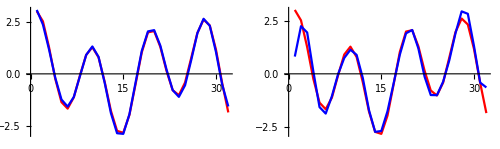

```mathematica
GraphicsGrid[{{ DecompressDCT, DecompressDFT}},ImageSize-> 500,PlotRange-> All]
```

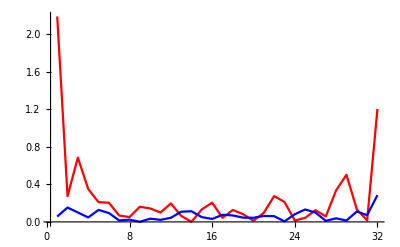

```mathematica
ListPlot[{Abs[Samp3-InverseCompressDFT3],Abs[Samp3-InverseCompressDCT3]},Joined-> True,PlotStyle-> {Red,Blue},PlotRange-> All]
```

Obviously keeping the same amount of data from the DCT of the signal produces much better approximation than keeping the same amount of data using DFT.

IMAGES: THE  2D CASE

```mathematica
imagein=Import["lena512.bmp"]
```

-Graphics-

```mathematica
imagemat=ImageData[imagein];
```

```mathematica
Dimensions[imagemat]
```

{512,512,3}

```mathematica
imageBW=imagemat[[;;,;;,1]];
```

```mathematica
Dimensions[imageBW]
```

{512,512}

```mathematica
II=ImageTake[imagein,{250,290},{250,350}]
```

-Graphics-

```mathematica
ImageTake[imagein,{250,290},{250,300}]
```

-Graphics-

```mathematica
ImageTake[imagein,{264,271},{264,271}]
```

-Graphics-

```mathematica
detail=imageBW[[264;;271,264;;271]]
```

{{0.196078,0.156863,0.180392,0.188235,0.298039,0.243137,0.270588,0.368627},{0.176471,0.152941,0.141176,0.156863,0.345098,0.341176,0.254902,0.337255},{0.188235,0.14902,0.141176,0.152941,0.219608,0.352941,0.254902,0.196078},{0.298039,0.188235,0.160784,0.168627,0.270588,0.439216,0.301961,0.219608},{0.352941,0.282353,0.258824,0.258824,0.352941,0.423529,0.290196,0.207843},{0.384314,0.337255,0.337255,0.356863,0.32549,0.282353,0.223529,0.258824},{0.309804,0.341176,0.352941,0.313725,0.301961,0.215686,0.254902,0.443137},{0.223529,0.211765,0.239216,0.227451,0.254902,0.301961,0.419608,0.627451}}

```mathematica
block=Floor[255detail];
```

```mathematica
Dimensions[block]
```

```mathematica
Image[block/255,ImageSize-> 300]
```

```mathematica
K=8;
```

```mathematica
block//MatrixForm
```

(50 | 40 | 46 | 48 | 76 | 62 | 69 | 94
45 | 39 | 36 | 40 | 88 | 87 | 65 | 86
48 | 38 | 36 | 39 | 56 | 90 | 65 | 50
76 | 48 | 41 | 43 | 69 | 112 | 77 | 56
90 | 72 | 66 | 66 | 90 | 108 | 74 | 53
98 | 86 | 86 | 91 | 83 | 72 | 57 | 66
79 | 87 | 90 | 80 | 77 | 55 | 65 | 113
57 | 54 | 61 | 58 | 65 | 77 | 107 | 160)

We first shift the data around the mean value 128 so that we get both positive and negative numbers between -128 and 127.

```mathematica
blockShift=block-128;
```

```mathematica
blockShift//MatrixForm
```

(-78 | -88 | -82 | -80 | -52 | -66 | -59 | -34
-83 | -89 | -92 | -88 | -40 | -41 | -63 | -42
-80 | -90 | -92 | -89 | -72 | -38 | -63 | -78
-52 | -80 | -87 | -85 | -59 | -16 | -51 | -72
-38 | -56 | -62 | -62 | -38 | -20 | -54 | -75
-30 | -42 | -42 | -37 | -45 | -56 | -71 | -62
-49 | -41 | -38 | -48 | -51 | -73 | -63 | -15
-71 | -74 | -67 | -70 | -63 | -51 | -21 | 32)

The DCT in two dimensions is done my doing the DCT in each dimension consecutively, i.e., first row wise and then column wise (or the other way around)

```mathematica
K=8;
```

```mathematica
1/(√K)∑_(i=0)^(K-1) 1/(√K)(∑_(j=0)^(K-1) A[[i+1,j+1]] Cos[(π (j +1/2)m)/K])Cos[(π (i +1/2)k)/K]=1/K∑_(i=0)^(K-1) ∑_(j=0)^(K-1) A[[i+1,j+1]] Cos[(π (j +1/2)m)/K]Cos[(π (i +1/2)k)/K]
```

```mathematica
With[{j=2,i=3},TB=N[Table[Cos[(π (j +1/2)m)/K]Cos[(π (i +1/2)k)/K],{k,0,7},{m,0,7}]]];
```

```mathematica
ListPlot3D[TB]
```

-Graphics3D-

```mathematica
dct=Table[N[1/K∑_(i=0)^(K-1) ∑_(j=0)^(K-1) blockShift[[i+1,j+1]]Cos[(π (i +1/2)k)/K] Cos[(π (j +1/2)m)/K]],{k,0,K-1},{ m,0,K-1}]
```

{{-466.75,-45.8515,13.6312,23.0686,10.7834,-14.6249,16.7408,0.844643},{-52.9448,-11.6912,-12.1557,23.8464,-4.41185,-2.29565,1.4106,1.91912},{1.43307,-27.3315,17.4165,-32.8659,14.8115,-7.76367,-4.13204,6.57798},{21.2361,29.1001,-10.2315,-6.19913,8.04654,-1.3821,-3.51096,3.50959},{6.36396,-16.9637,7.95826,7.84459,-3.,3.59987,1.57434,0.821373},{-6.45242,9.1618,2.89879,-6.66503,0.0106693,2.44806,-0.384602,-0.435838},{-9.01263,2.43355,0.242956,-1.48097,-1.80556,7.29704,-0.7915,-2.43189},{-3.30568,3.13619,-1.93611,-2.66837,-3.08341,-0.074948,-1.27566,0.69229}}

For the inverse transformation we have

```mathematica
a[k_]:=If[k==0,1/2,1];
```

```mathematica
idct=Table[Chop[4/K(∑_(i=0)^(K-1) ∑_(j=0)^(K-1) a[i]a[j]dct[[i+1,j+1]]Cos[(π (k +1/2)i)/K] Cos[(π (m +1/2)j)/K])],{k,0,K-1},{m,0,K-1}];
```

```mathematica
idct//MatrixForm
```

(-78. | -88. | -82. | -80. | -52. | -66. | -59. | -34.
-83. | -89. | -92. | -88. | -40. | -41. | -63. | -42.
-80. | -90. | -92. | -89. | -72. | -38. | -63. | -78.
-52. | -80. | -87. | -85. | -59. | -16. | -51. | -72.
-38. | -56. | -62. | -62. | -38. | -20. | -54. | -75.
-30. | -42. | -42. | -37. | -45. | -56. | -71. | -62.
-49. | -41. | -38. | -48. | -51. | -73. | -63. | -15.
-71. | -74. | -67. | -70. | -63. | -51. | -21. | 32.)

```mathematica
NumberForm[blockShift//MatrixForm,3]
```

```mathematica
Q={{16,11, 10,16,24,40,51,61},{12,12,14,19,26,58,60,55},{14,13,16,24,40,57,69,56},{14,17,22,29,51,87,80,62},
{18,22,37,56,68,109,103,77},{24,35,55,64,81,104,113,92},{49,64,78,87,103,121,120,101},{72,92,95,98,112,100,103,99}};
```

```mathematica
Q//MatrixForm
```

(16 | 11 | 10 | 16 | 24 | 40 | 51 | 61
12 | 12 | 14 | 19 | 26 | 58 | 60 | 55
14 | 13 | 16 | 24 | 40 | 57 | 69 | 56
14 | 17 | 22 | 29 | 51 | 87 | 80 | 62
18 | 22 | 37 | 56 | 68 | 109 | 103 | 77
24 | 35 | 55 | 64 | 81 | 104 | 113 | 92
49 | 64 | 78 | 87 | 103 | 121 | 120 | 101
72 | 92 | 95 | 98 | 112 | 100 | 103 | 99)

```mathematica
DCT=Table[Round[dct[[i,j]]/Q[[i,j]]],{i,1,K},{j,1,K}];
```

```mathematica
DCT//MatrixForm
```

(-29 | -4 | 1 | 1 | 0 | 0 | 0 | 0
-4 | -1 | -1 | 1 | 0 | 0 | 0 | 0
0 | -2 | 1 | -1 | 0 | 0 | 0 | 0
2 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The above matrix is then encoded using standard lossless compression algorithms such as the zero run and Huffman encoding. 
To decompress the image we now reverse the operations. First we multiply the entries with the corresponding entries of the matrix Q:

```mathematica
DCTQ=Table[DCT[[i,j]]Q[[i,j]],{i,1,K},{j,1,K}];
```

We then apply the Inverse DCT:

```mathematica
IDCT=Table[Round[4/K(∑_(i=0)^(K-1) ∑_(j=0)^(K-1) a[i]a[j]DCTQ[[i+1,j+1]]Cos[(π (k +1/2)i)/K] Cos[(π (m +1/2)j)/K])],{k,0,K-1},{m,0,K-1}];
```

```mathematica
IDCT//MatrixForm
```

(-81 | -82 | -80 | -72 | -61 | -50 | -44 | -41
-80 | -85 | -86 | -76 | -62 | -53 | -54 | -59
-82 | -91 | -94 | -79 | -56 | -46 | -55 | -69
-73 | -84 | -88 | -71 | -46 | -36 | -49 | -67
-40 | -53 | -61 | -55 | -42 | -40 | -54 | -70
-17 | -26 | -37 | -45 | -50 | -55 | -61 | -65
-43 | -41 | -43 | -52 | -62 | -59 | -44 | -29
-88 | -75 | -64 | -66 | -69 | -53 | -16 | 15)

Finally we shift back the values by adding 128 to all entries

```mathematica
IDCTS=IDCT+128;
```

```mathematica
IDCTS//MatrixForm
```

(47 | 46 | 48 | 56 | 67 | 78 | 84 | 87
48 | 43 | 42 | 52 | 66 | 75 | 74 | 69
46 | 37 | 34 | 49 | 72 | 82 | 73 | 59
55 | 44 | 40 | 57 | 82 | 92 | 79 | 61
88 | 75 | 67 | 73 | 86 | 88 | 74 | 58
111 | 102 | 91 | 83 | 78 | 73 | 67 | 63
85 | 87 | 85 | 76 | 66 | 69 | 84 | 99
40 | 53 | 64 | 62 | 59 | 75 | 112 | 143)

Compare this with the original block:

```mathematica
block//MatrixForm
```

(50 | 40 | 46 | 48 | 76 | 62 | 69 | 94
45 | 39 | 36 | 40 | 88 | 87 | 65 | 86
48 | 38 | 36 | 39 | 56 | 90 | 65 | 50
76 | 48 | 41 | 43 | 69 | 112 | 77 | 56
90 | 72 | 66 | 66 | 90 | 108 | 74 | 53
98 | 86 | 86 | 91 | 83 | 72 | 57 | 66
79 | 87 | 90 | 80 | 77 | 55 | 65 | 113
57 | 54 | 61 | 58 | 65 | 77 | 107 | 160)

We can compute the difference between the original and decompressed image:

```mathematica
(block-IDCTS)//MatrixForm
```

(3 | -6 | -2 | -8 | 9 | -16 | -15 | 7
-3 | -4 | -6 | -12 | 22 | 12 | -9 | 17
2 | 1 | 2 | -10 | -16 | 8 | -8 | -9
21 | 4 | 1 | -14 | -13 | 20 | -2 | -5
2 | -3 | -1 | -7 | 4 | 20 | 0 | -5
-13 | -16 | -5 | 8 | 5 | -1 | -10 | 3
-6 | 0 | 5 | 4 | 11 | -14 | -19 | 14
17 | 1 | -3 | -4 | 6 | 2 | -5 | 17)

```mathematica
I1=Image[block/255,ImageSize-> 400]; I2=Image[IDCTS/255,ImageSize-> 400];
```

```mathematica
E1=Image[ConstantArray[1,{8,8}]-Abs[block-IDCTS]/255,ImageSize-> 100];
```

What is the visual impact of compression can be seen below

```mathematica
GraphicsGrid[{{I1,I2,E1}},ImageSize-> 600,Frame->All]
```

-Graphics-